```mathematica
ClearAll
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

(A √(3/(-1/4+Log[4/3])))/(32 π √(A/s^4) s^3)

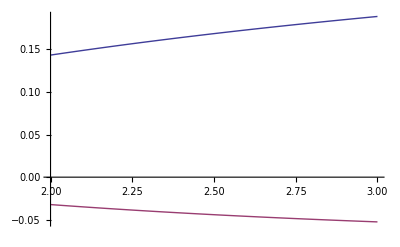

{A→(4 π^2 s^4 (1+K^2 s^2) σo^2)/(-K^2 s^2+(1+K^2 s^2) Log[1+K^2 s^2])}

{A→9.05477×10^6 Mpc^4}

0.586672 √(-1+1/(1+(100 π^2)/R^2)+Log[1+(100 π^2)/R^2])

```mathematica
Remove["Global`*"]
σ=√((1/(2 π^2))Integrate[(A k^3)/((1+k^2 s^2)^2),{k,0,K},Assumptions->{s>0,K>0}]);
Limit[σ,K->∞];
Series[σ,{K,∞,1}];
Limit[σ,K->0];
Series[σ,{K,0,9}];

dk=D[σ,{K,1}];
dk2=dk/.K->1/(√3 s)
Plot[{σ/.A->1/.s->1,(dk-dk2)/.A->1/.s->1},{K,2,3},GridLines->{{π/(2/√3)},None}]
Solve[σ==σo,A][[1]]//PowerExpand//FullSimplify
%/.s->(20 h^-1 Mpc)/.K->π/(2(8 h^-1 Mpc))/.σo->.8/.h->.7
σp[R_]=σ/.%/.s->(20 h^-1 Mpc)/.K->π/(2( R h^-1 Mpc ))/.σo->.8/.h->.7//FullSimplify
```

```mathematica
σp[.8]
σp[8]
σp[80]
```

1.47746

0.8

0.0581068

```mathematica
Log10[(9.054773282092059*^6 (1/(8 .7)))/(1+(20/8)^2)]
Log10[1/(8 .7)]//N
```

5.34835

-0.748188

```mathematica
Remove["Global`*"]
```

1.38889

```mathematica
(1.69/4)^(1.5/6) //N
```

0.806226

1.78865

0.618698

2.73154

```mathematica
Di={1.63,2};
Ω={.3,1};
(4π)/3*( Ω((2.78*10^11)))(8)^3
{.8,.5}((5*10^14)/%)^(-1/4);
1.69/%
√(2/π)(Ω (2.78*10^11))/(5*10^14) (1/4)% Exp[-(%^2)/2]//ScientificForm
%[[2]]/%[[1]] //N
```

{1.78865×10^14,5.96216×10^14}

{2.73154,3.23451}

{2.1791×10^-6,1.91848×10^-6}

0.880402

```mathematica
σe/.NSolve[.3 2.7315431377463777 Exp[-(2.7315431377463777)^2 /2]==(1.69/(σe))Exp[-(1.69/σe)^2 /2],σe][[1]]
(4π)/3*( ((2.78*10^11)))(8)^3
Solve[%%==σe((5*10^14)/%)^(-1/4),σe]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.52968

5.96216×10^14

{{σe→0.50688}}

```mathematica
Remove["Global`*"]
V=(((1.48^2)(2.998*10^5)^3)/((100^3) 4.3))(60^2/206265^2).5//N;
np=.068
√(2/π)(.3 (2.78*10^11))/(np) ((3-2)/6)ν Exp[-(ν^2)/2]
Series[%,{ν,a,2}]//Normal//Expand//Simplify
nu=ν/.NSolve[%==10^12,ν][[1]];
σ=(2.15/3.13)(Mmax/10^12)^(-1/6)
Solve[nu==1.69/σ,Mmax];
Mmax=Mmax/.%;
```

0.068

1.63097×10^11 ⅇ^(-ν^2/2) ν

ⅇ^(-a^2/2) (8.15485×10^10 a^5+1.63097×10^11 ν+3.26194×10^11 a^2 ν-1.63097×10^11 a^4 ν-2.44645×10^11 a ν^2+a^3 (-8.15485×10^10+8.15485×10^10 ν^2))

68.6901/Mmax^(1/6)

```mathematica
1/(.8/3.13)
(((%-1)1.69)+1)^(1/2)
Solve[%==nu((10^12)/M)^(1/6)]
Solve[%%==nu(Mmax/M)^(1/6)]
```

3.9125

2.43354

{{M→5.31256×10^8}}

{{M→264293.}}

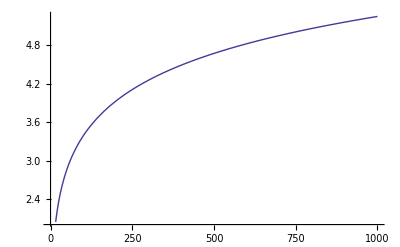

```mathematica
Plot[ProductLog[x],{x,0,1000}]
```

```mathematica
Remove["Global`*"]
M=2*10^33;
R=10^6;
B=10^12;
α=π/2;
P[w_]=(2 w^4 B^2 R^6 Sin[α]^2)/(3(3*10^10)^3)//N
Τ[w_]=(3 (3*10^10)^3 M)/(B^2 R^4 w^2 Sin[α]^2)//N
P[{10^4,10^3,10^2}]
Τ[{10^4,10^3,10^2}]
```

2.46914×10^28 w^4

(1.62×10^17)/w^2

{2.46914×10^44,2.46914×10^40,2.46914×10^36}

{1.62×10^9,1.62×10^11,1.62×10^13}

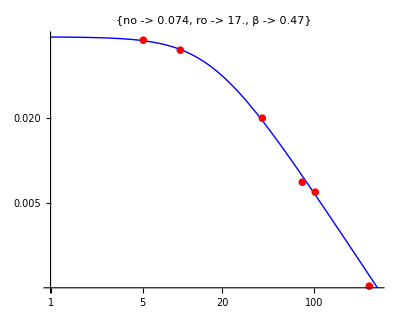

ϵff[r_] = 1.34157×10^-23 √kT ne^2

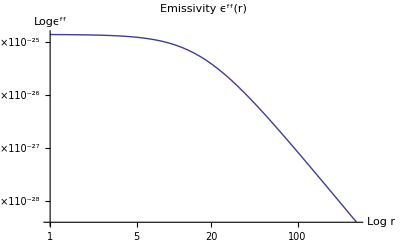

τ_c = 3.01887×10^15 (1+0.00365589 r^2)^0.700729

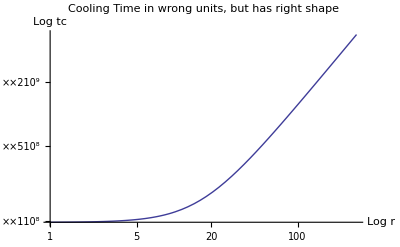

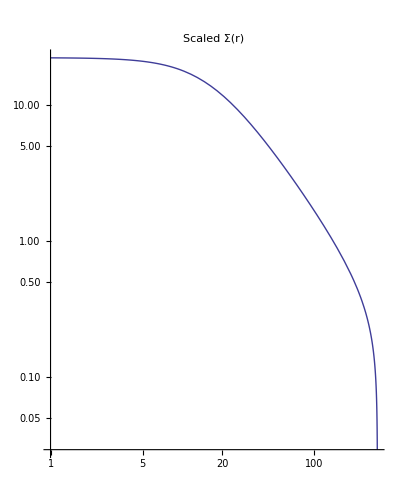

```mathematica
Remove["Global`*"]
dat={{5,.07},{9.5,.06},{40,.02},{80,.007},{100,.006},{260,.0013}};
model=no/((1+(r/ro)^2)^(3 β/2));
nlm=NonlinearModelFit[dat,{model},{no,ro,β},{r}];
f[r_]=Normal[nlm];
parm=NumberForm[nlm["BestFitParameters"],2];
pf:=LogLogPlot[f[r],{r,1,300},PlotStyle->{Thick,Blue}]
pd:=ListLogLogPlot[dat,PlotMarkers->{Automatic,10},PlotStyle->Red]
Show[pf,pd,AspectRatio->.8,PlotLabel->Style[ToString[parm],12,Bold,"Graphics"]]
B=(π 2 (kT 1.602*10^-9))/((6.626*10^-27)^2(2.998*10^10)^2) (1/(Exp[kT/kT]-1));
jff[r_]= (1.7*10^-25((kT*1.602*10^-9)/(1.38*10^-16))^(-7/2)(1.25^2)f[r]^2(3/2) B)//N;
Print["ϵff[r_] = ",ϵff[r_]=(1.4*10^-27)((kT*1.602*10^-9)/(1.38*10^-16))^(1/2)ne^2(3/2)(1.25^2)(1.2)]
ϵff[r_]=ϵff[r]/.kT->(3.5)/.ne->f[r];
LogLogPlot[ϵff[r],{r,1,300},PlotLabel->"Emissivity ϵ^ff(r)",AxesLabel->{"Log r","Logϵ^ff"}]
eng=f[r] (kT*1.602*10^-9); 
Print["τ_c = ",tc[r_]=((ϵff[r]/eng))^-1/.kT->(3.5)]
LogLogPlot[tc[r]/(π*10^7),{r,1,300},PlotLabel->"Cooling Time in wrong units, but has right shape",AxesLabel->{"Log r","Log tc"}]

LogLogPlot[f[r] √(300^2-r^2),{r,1,300},PlotLabel->"Scaled Σ(r)",AspectRatio->1.25]
```

```mathematica
,
```

```mathematica
B=(2 6.626*10^-27 ν^3)/c^2 (1/(Exp[(h ν)/kT]-1))
Integrate[B,{ν,0,∞}]
```

(2 h ν^3)/(c^2 (-1+ⅇ^((h ν)/kT)))

ConditionalExpression[(2 kT^4 π^4)/(15 c^2 h^3),Re[h/kT]>0]

```mathematica
eng/.kT->3.5
```

{6.93231×10^13,2.05789×10^16}

```mathematica
π/32400//N
```

```mathematica
0.0000969627362219072*440(3/2)
```

0.0639954

```mathematica
1/2000//N
```

0.0005

```mathematica
.45*60
```

27.

```mathematica
π 320 (2π 206265)(a1/206265)
π 290 (2π 206265)(a2/206265)
Solve[%%==%]
```

640 a1 π^2

580 a2 π^2

{{a1→(29 a2)/32}}

```mathematica
(8.235*10^-2 (10^4 1.13)^-1.35(50)^-2.1(.8 10^5))/(.66*10^-24)
LogLogPlot[(8.235*10^-2 (10^4 T4)^-1.35(50)^-2.1(.8 10^5))/(.66*10^-24),{T4,1,100}]
```

9.11416×10^18